```mathematica
ωρ= 2 π 1020;
ωz = 2 π 55;
MHe=4.0026032*1.66053886 10^-27
```

6.64648×10^-27

```mathematica
ℏ=1.05457148 10^-34
```

1.05457×10^-34

```mathematica
aHe=7.51 10^-9
```

7.51×10^-9

```mathematica
UHe=(4π ℏ^2 aHe)/MHe
```

1.5791×10^-49

```mathematica
Nparticles = 2 10^6
```

2000000

```mathematica
ωρ=2π 1020
ωz = 2π 55
```

2040 π

110 π

```mathematica
ω3D = ωρ^2 ωz
```

457776000 π^3

```mathematica
μ = ((15 Nparticles UHe ω3D)/(8π))^(2/5)(MHe/2)^(3/5)
```

1.21309×10^-29

```mathematica
g = 9.8
```

9.8

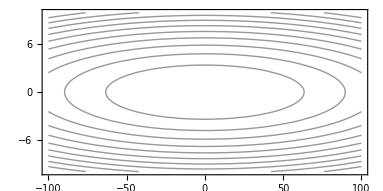

```mathematica
ContourPlot[1/2 ωρ^2 ρ^2+1/2 ωz^2 z^2,{z,-100 ,100 },{ρ,-10,10},AspectRatio->1/2,ContourShading->None,Contours->10,PlotRangePadding->None]
```

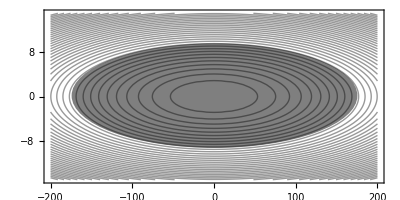

```mathematica
Show[ContourPlot[1/2 ωρ^2 ρ^2+1/2 ωz^2 z^2,{z,-200 ,200 },{ρ,-15,15},AspectRatio->1/2,ContourShading->None,Contours->40,PlotRangePadding->None,FrameStyle->14],Graphics[{Opacity[0.5],Disk[{0, g/ωρ^2 10^6}, {1/ωz √((2μ)/MHe)10^6,1/ωρ √((2μ)/MHe)10^6}]}]]
```